# PDEs

Partial Differential Equations (PDEs) are the source of most (but far from all) large scale linear algebra problems. We are going to discretize one standard PDE with a few techniques.

## Laplacian -Δu=f

This means in 1D Cartesian coordinates x our Dirichlet problem is to find a function satisfying 
	-u_xx=f 
on an interval a<x<b with u(a) and u(b) specified.  We are going to do the 1D problem first.

This means in 2D Cartesian coordinates (x, y) that we are trying to find a function satisfying
	-Δu=-(u_xx+u_yy)=f(x,y)
on some domain Ω⊂ℝ^2 with suitable boundary conditions on the boundary ∂Ω.  The simplest conditions are Dirichlet conditions 
	u(x,y)=g(x,y)  for {x,y}∈∂Ω. 
Other boundary conditions are common. Dirichlet is easiest to understand.

This means in 3D Cartesian coordinates (x, y) that we are trying to find a function satisfying
	-Δu=-(u_xx+u_yy+u_zz)=f(x,y,z)
on some domain Ω⊂ℝ^3 with suitable boundary conditions on the boundary ∂Ω.  The simplest conditions are Dirichlet conditions 
	u(x,y,z)=g(x,y,z)  for {x,y,z}∈∂Ω. 
Other boundary conditions are common. Dirichlet is easiest to understand.

### 1D: Centered Finite Differences

We are going to approximate the solution for
	-u_xx=f(x^2)   for x∈(0,1) and u(0)=α and u(1)=β
by splitting the interval up into equally spaced subintervals.  Define
	Δx=1/(n+1) and x_i=i Δx for i=0,…,n
so that the end points are x_0=0  and x_(n+1)=1.  In this finite difference context the discretization points x_i are called nodes. Approximate the second derivative using the standard second difference
	u_xx(x_i)=(u(x_(i-1))-2 u(x_i)+u(x_(i+1)))/Δx^2
and substitute into the equation at the interior points and multiply by -Δx^2 to get 
	u(x_(i-1))-2 u(x_i)+u(x_(i+1)) | = | -Δx^2f(x_i) for i=1:n
while the boundary conditions give 
	u(x_0)=α and u(x_(n+1))=β.
The solution of the linear system 
	-2 u_1 | + | u_2 | + |   |   |   |   |   |   | = | -Δx^2f(x_1) | - | α
u_1 | - | 2 u_2 | + | u_3 |   |   |   |   |   | = | -Δx^2f(x_2) |   |  
  |   | u_2 | + | -2 u_3 | + | u_4 |   |   |   | = | -Δx^2f(x_3) |   |  
  |   |   |   |   | ⋱ |   |   |   |   | ⋮ | ⋮ |   |  
  |   |   |   |   | u_(n-2) | + | -2 u_(n-1) | + | u_n | = | -Δx^2f(x_(n-1)) |   |  
  |   |   |   |   |   |   | u_(n-1) | + | -2 u_n | = | -Δx^2f(x_(n-1)) | - | β
gives an approximation u_i≈u(x_i).  The approximation gets better as Δx gets smaller or equivalently n gets bigger.  Hopefully this is obviously the solution of the linear system
	A.u=b
where A is the symmetric tridiagonal matrix with -2 on the diagonal and 1 on the off diagonals.

```mathematica
uSol[x_]:=x Cos[x]-x^3;
{α,β}={uSol[0],uSol[1]};
f[x_]=-D[uSol[x],{x,2}];
m=100; Δx=1.0/(m+1);
A=SparseArray[{Band[{1,1}]->-2.0,Band[{2,1}]->1,Band[{1,2}]->1},{m,m}];
b=-Δx^2 Table[f[i Δx],{i,1,m}];b⟦{1,m}⟧-={α,β};
u=LinearSolve[A,b]; uBC=Join[{α},u,{β}];
TabView[{
"Sol"->Show[
Plot[ uSol[x],{x,0,1},PlotStyle->Red],
ListPlot[uBC,DataRange->{0,1}],
PlotLabel->m
],
"Error"->ListPlot[u-Table[uSol[i Δx],{i,m}],PlotLabel->m]
}]
```

12

It is more complicated to do this in 2D or 3D because numbering the nodes is less simple.

### 2D: Centered Finite Differences

The simplest possible 2D domain is a square Ω=(0,1)×(0,1)⊂ℝ^2 with n points in each direction! Define 
	h=1/(n+1)
	p_(i,j)=h{i,j}
The equivalent approximation schemes are 
	u_xx(p_(i,j))≈(u(p_(i-1,j))-2u(p_(i,j))+u(p_(i+1,j)))/h^2
and  
	u_yy(p_(i,j))≈(u(p_(i,j-1))-2u(p_(i,j))+u(p_(i,j+1)))/h^2.
The approximation for -Δ you get by summing these two is frequently presented as the “stencil”
	0 |     1 | 0
1 | -4 | 1
0 |     1 | 0
In the abstract our equations are relatively simple again
	-4 u_(i,j)+u_(i-1,j)+u_(i+1,j)+u_(i,j-1)+u_(i,j+1)==-h^2f(p_(i,j))  for i=1:n and j=1:n
The boundary conditions now look like
	u_(0,j)=g(p_(0,j)) and u_(n+1,j)=g(p_(n+1,j))  for j=0:n+1
and 
	u_(i,0)=g(p_(i,0)) and u_(i,n+1)=g(p_(i,n+1))for i=0:n+1.
There are four different edges and four corners where edges meet.  This is harder to implement than the 1D version!  It is largely bookkeeping but it is important bookkeeping.  It turns out that the boundary conditions cause most of the organizational grief! As we will find out different PDE packages deal with the bookkeeping in different ways.  I found out last week that software Kyle uses enforces Dirichlet boundary conditions by putting a very simple equation into the matrix for each boundary node.   If we do the same we will have m=(n+2)^2 nodes and we will get an m×m matrix.

The first thing to do is work out some way to number the nodes. We need to identify the interior nodes. We need to identify the boundary nodes.

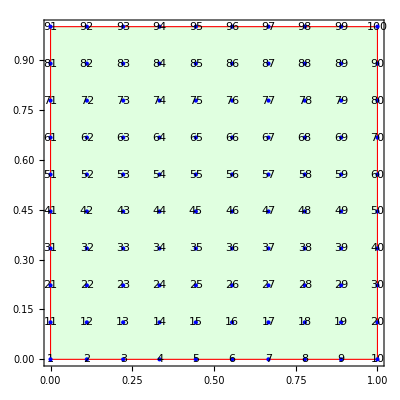

```mathematica
n=8; h=1/(n+1); m=(n+2)^2;
ijTok[i_,j_]:=1+i+(n+2)j
p[i_,j_]:={i h,j h}
Graphics[{
{LightGreen,EdgeForm[Red],Rectangle[{0,0},{1,1}]},
Table[
{Text[ijTok[i,j],p[i,j]],{Blue,Point[p[i,j]]}},
{i,0,n+1},{j,0, n+1}]
},
AspectRatio->Automatic,
Frame->True]
```

Identify the boundary points in class.

```mathematica
Clear[u,f]
u[{x_,y_}]:=Sin[x y]+x^2
f[{x_,y_}]=Laplacian[u[{x,y}],{x,y}];
n=4;h=1.0/(n+1); m=(n+2)^2;
ijTok[i_,j_]:=1+i+(n+2)j
p[i_,j_]:={i h,j h}
A=SparseArray[{},{m,m}];
b=ConstantArray[0,m];
(* Interior Nodes - Laplacian *)
Do[
kM=ijTok[i,j];
kU= ijTok[i,j+1];
kD= ijTok[i,j-1];
kL= ijTok[i+1,j];
kR= ijTok[i-1,j];
A⟦kM,kM⟧=-4.0;
A⟦kM,kU⟧=A⟦kM,kD⟧=A⟦kM,kL⟧=A⟦kM,kR⟧=1.0;
b⟦kM⟧=-h^2 f[p[i,j]],
{i,1,n},{j,1,n}];
(* Boundary Nodes - Dirichlet - Deal II style *)
Do[
kM=ijTok[i,j];
A⟦kM,kM⟧=1;
b⟦kM⟧=u[p[i,j]],
{i,{0,n+1}},{j,0,n+1}];
Do[
kM=ijTok[i,j];
A⟦kM,kM⟧=1;
b⟦kM⟧=u[p[i,j]],
{i,0,n},{j,{0,n+1}}];

(* What do the matrix A and RHS look like? *)
TabView[{
"A"->MatrixPlot[A,Mesh->All,PlotLegends->Automatic],
"λ(A)"->ListPlot[ReIm[Eigenvalues[A]],PlotRange->All,Frame->True],
"b"->ListPlot[b,PlotRange->All]}]
```

123

Fix the eigenvalue signs!

```mathematica
Clear[u,f]
u[{x_,y_}]:=Sin[x y]+x^2
f[{x_,y_}]=-Laplacian[u[{x,y}],{x,y}];
n=60;h=1/(n+1); m=(n+2)^2;
ijTok[i_,j_]:=1+i+(n+2)j
p[i_,j_]:={i h,j h}
A=SparseArray[{},{m,m}];
b=ConstantArray[0,m];
(* Interior Nodes - Laplacian *)
Do[
kM=ijTok[i,j];
kU= ijTok[i,j+1];
kD= ijTok[i,j-1];
kL= ijTok[i+1,j];
kR= ijTok[i-1,j];
A⟦kM,kM⟧=-4.0;
A⟦kM,kU⟧=A⟦kM,kD⟧=A⟦kM,kL⟧=A⟦kM,kR⟧=1.0;
b⟦kM⟧=-h^2 f[p[i,j]],
{i,1,n},{j,1,n}];
(* Boundary Nodes - Dirichlet - Deal II style *)
Do[
kM=ijTok[i,j];
A⟦kM,kM⟧=-1;
(* Signs are flipped to make evals the same sign *)
b⟦kM⟧=-u[p[i,j]],
{i,{0,n+1}},{j,0,n+1}];
Do[
kM=ijTok[i,j];
(* Signs are flipped to make evals the same sign *)
A⟦kM,kM⟧=-1;
b⟦kM⟧=-u[p[i,j]],
{i,0,n+1},{j,{0,n+1}}];
(* Compare u and approximation U RHS? *)
uMat=Table[u[p[i,j]],{i,0,n+1},{j,0,n+1}];
U = Partition[LinearSolve[A,b],n+2];
TabView[{
"u"->ContourPlot[u[{x,y}],{x,0,1},{y,0,1},PlotLegends->Automatic],
(* Explain Transpose *)
"uMat"->ListContourPlot[uMatᵀ,DataRange->{{0,1},{0,1}},PlotLegends->Automatic],
"U"->ListContourPlot[U,DataRange->{{0,1},{0,1}},PlotLegends->Automatic],
"U-uMat"->ListContourPlot[U-uMatᵀ,DataRange->{{0,1},{0,1}},PlotLegends->Automatic],
λs=Quiet[Eigenvalues[-A]];
"λ(-A)"->ListPlot[ReIm[λs],PlotRange->All],
"λ(-A)"->ListPlot[λs,PlotRange->All]
}]
Dimensions[U]
```

123456

{62,62}

```mathematica
ListPlot3D
```

ListPlot3D

```mathematica
Clear[uSol,x,y,p]
uSol[{x_,y_}]:=x Cos[x y]-x^3+Sin[y]Cos[Sin[x^2+y]+y];
f[{x_,y_}]=-(D[uSol[{x,y}],{x,2}]+D[uSol[{x,y}],{y,2}]);
n=12; h=1.0/(n+1);
p[i_,j_]:=h{i,j};
m=n^2;
A=SparseArray[{},{m,m}];b=ConstantArray[0,m];
k[i_,j_]:=i+n(j-1)
```

k is just a choice of numbering scheme for the points p_(i,j)!

```mathematica
Table[k[i,j],{i,1,n},{j,1,n}]
```

{{1,13,25,37,49,61,73,85,97,109,121,133},{2,14,26,38,50,62,74,86,98,110,122,134},{3,15,27,39,51,63,75,87,99,111,123,135},{4,16,28,40,52,64,76,88,100,112,124,136},{5,17,29,41,53,65,77,89,101,113,125,137},{6,18,30,42,54,66,78,90,102,114,126,138},{7,19,31,43,55,67,79,91,103,115,127,139},{8,20,32,44,56,68,80,92,104,116,128,140},{9,21,33,45,57,69,81,93,105,117,129,141},{10,22,34,46,58,70,82,94,106,118,130,142},{11,23,35,47,59,71,83,95,107,119,131,143},{12,24,36,48,60,72,84,96,108,120,132,144}}

It is fairly easy to put all the RHS function values from f[x,y] into the RHS vector b. The boundary condition terms are trickier.

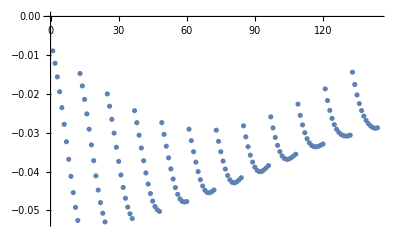

```mathematica
Do[b⟦k[i,j]⟧=-h^2 f[p[i,j]],{i,n},{j,n}];
ListPlot[b]
```

It is fairly easy to put the matrix entries into the correct places.

```mathematica
A=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{n^2,n^2}];
b=ConstantArray[0,n^2];
b=-Δx^2 Table[f[i Δx],{i,1,m}];b⟦{1,m}⟧-={α,β};
u=LinearSolve[A,b]; uBC=Join[{α},u,{β}];
TabView[{
"Sol"->Show[
Plot[ uSol[x],{x,0,1},PlotStyle->Red],
ListPlot[uBC,DataRange->{0,1}],
PlotLabel->m
],
"Error"->ListPlot[u-Table[uSol[i Δx],{i,m}],PlotLabel->m]
}]
```

12

It is more complicated to do this in 2D because numbering the approximation points is less simple.

### 3D: Centered Finite Differences

The simplest possible 3D domain is a square Ω=(0,1)×(0,1)×(0,1)⊂ℝ^3 with n points in each direction! Define 
	h=1/(n+1)
	p_(i,j,k)=h{i,j,k}
The equivalent approximation schemes are 
	u_xx(p_(i,j,k))≈(u(p_(i-1,j,k))-2u(p_(i,j,k))+u(p_(i+1,j,k)))/h^2
and similarly for the y and z directions. Summing the three directions gives the “stencil” with 1s in 6 directions and a -6 in the middle.

It is easier to write code than to explain in words.

The first thing to do is work out some way to number the nodes. We need to identify the interior nodes. We need to identify the boundary nodes.

```mathematica
n=4; h=1/(n+1); m=(n+2)^3;
ijkToNodeNumber[i_,j_,k_]:=1+i+(n+2)j+(n+2)^2 k
p[i_,j_,k_]:={i h,j h,k h}
TabView[{
"Dots & Numbers"->Graphics3D[{
{LightGreen,Opacity[0.5],EdgeForm[Red],Cuboid[{0,0,0},{1,1,1}]},
Table[
num=ijkToNodeNumber[i,j,k];
{Hue[num/(n+2)^3],Text[num,p[i,j,k]],Point[p[i,j,k]]},
{i,0,n+1},{j,0, n+1},{k,0,n+1}]
}],
"Dots"->Graphics3D[{
{LightGreen,Opacity[0.5],EdgeForm[Red],Cuboid[{0,0,0},{1,1,1}]},
Table[
num=ijkToNodeNumber[i,j,k];
{Hue[num/(n+2)^3],Point[p[i,j,k]]},
{i,0,n+1},{j,0, n+1},{k,0,n+1}]
}]},2]
```

Set up a test problem

```mathematica
Clear[u,f]
u[{x_,y_,z_}]:=Sin[x y+z]+x^2- x z
f[{x_,y_,z_}]=Laplacian[u[{x,y,z}],{x,y,z}];
n=12;h=1.0/(n+1); m=(n+2)^3;
ijkToNodeNumber[i_,j_,k_]:=1+i+(n+2)j+(n+2)^2 k
p[i_,j_,k_]:={i h,j h,k h}
A=SparseArray[{},{m,m}];
b=ConstantArray[0,m];
(* Interior Nodes - Laplacian *)
Do[
kM=ijkToNodeNumber[i,j,k];
kU= ijkToNodeNumber[i,j,k+1];
kD= ijkToNodeNumber[i,j,k-1];
kL= ijkToNodeNumber[i,j+1,k];
kR=ijkToNodeNumber[i,j-1,k];
kI= ijkToNodeNumber[i+1,j,k];
kO=ijkToNodeNumber[i-1,j,k];
A⟦kM,kM⟧=-6.0;
A⟦kM,kU⟧=A⟦kM,kD⟧=A⟦kM,kL⟧=A⟦kM,kR⟧=A⟦kM,kI⟧=A⟦kM,kO⟧=1.0;
b⟦kM⟧=-h^2 f[p[i,j,k]],
{i,1,n},{j,1,n},{k,1,n}];
(* Boundary Nodes - Dirichlet - Deal II style *)
Do[
kM=ijkToNodeNumber[i,j,k];
A⟦kM,kM⟧=-1;
b⟦kM⟧=-u[p[i,j,k]],
{i,{0,n+1}},{j,0,n+1},{k,0,n+1}];
Do[
kM=ijkToNodeNumber[i,j,k];
A⟦kM,kM⟧=-1;
b⟦kM⟧=-u[p[i,j,k]],
{i,0,n+1},{j,{0,n+1}},{k,0,n+1}];
Do[
kM=ijkToNodeNumber[i,j,k];
A⟦kM,kM⟧=-1;
b⟦kM⟧=-u[p[i,j,k]],
{i,0,n+1},{j,0,n+1},{k,{0,n+1}}];
(* What do the matrix A and RHS look like? *)
TabView[{
"A"->MatrixPlot[A,PlotLegends->Automatic],
"A_top"->MatrixPlot[A⟦1;;750,1;;750⟧,PlotLegends->Automatic],
"A_mid"->MatrixPlot[A⟦250;;500,250;;500⟧,PlotLegends->Automatic,DataRange->{{250,500},{250,500}}],
"b"->ListPlot[b,PlotRange->All]}]
```

1234

Actually approximately solve the PDE

```mathematica
Clear[u,f,x,y,z]
u[{x_,y_,z_}]:=Sin[x y+z]+x^2- x z
f[{x_,y_,z_}]=Laplacian[u[{x,y,z}],{x,y,z}];
n=12;h=1/(n+1); m=(n+2)^3;
ijkToNodeNumber[i_,j_,k_]:=1+i+(n+2)j+(n+2)^2 k
p[i_,j_,k_]:={i h,j h,k h}
A=SparseArray[{},{m,m}];
b=ConstantArray[0,m];
(* Interior Nodes - Laplacian *)
Do[
kM=ijkToNodeNumber[i,j,k];
kU= ijkToNodeNumber[i,j,k+1];
kD= ijkToNodeNumber[i,j,k-1];
kL= ijkToNodeNumber[i,j+1,k];
kR=ijkToNodeNumber[i,j-1,k];
kI= ijkToNodeNumber[i+1,j,k];
kO=ijkToNodeNumber[i-1,j,k];
A⟦kM,kM⟧=-6.0;
A⟦kM,kU⟧=A⟦kM,kD⟧=A⟦kM,kL⟧=A⟦kM,kR⟧=A⟦kM,kI⟧=A⟦kM,kO⟧=1.0;
b⟦kM⟧=-h^2 f[p[i,j,k]],
{i,1,n},{j,1,n},{k,1,n}];
(* Boundary Nodes - Dirichlet - Deal II style *)
Do[
kM=ijkToNodeNumber[i,j,k];
A⟦kM,kM⟧=-1;
b⟦kM⟧=-u[p[i,j,k]],
{i,{0,n+1}},{j,0,n+1},{k,0,n+1}];
Do[
kM=ijkToNodeNumber[i,j,k];
A⟦kM,kM⟧=-1;
b⟦kM⟧=-u[p[i,j,k]],
{i,0,n+1},{j,{0,n+1}},{k,0,n+1}];
Do[
kM=ijkToNodeNumber[i,j,k];
A⟦kM,kM⟧=-1;
b⟦kM⟧=-u[p[i,j,k]],
{i,0,n+1},{j,0,n+1},{k,{0,n+1}}];
(* Compare u and approximation U RHS? *)
x=LinearSolve[A,b];
U=Map[Partition[#,n+2]&,Partition[x,(n+2)^2]];
TabView[{
"U"->ListContourPlot3D[U,DataRange->{{0,1},{0,1},{0,1}},PlotLegends->Automatic],
"u"->ContourPlot3D[u[{x,y,z}],{x,0,1},{y,0,1},{z,0,1},PlotLegends->Automatic]
}]
```

12